# Generating Realistic Cities with Perlin Noise

## Abstract

Abstract

## Introduction

### What is Perlin noise?

Perlin noise is an algorithm that is often used in terrain generation within video games, originally created in 1983 by Ken Perlin. It is useful in generating natural-looking randomness with specific desirable properties which makes it perfect for simulating natural phenomena, which in our case will be cities.
	Perlin noise is continuous, repeatable(able to be tiled), and deterministic(gives the same output for a given input).

## Creating Perlin Noise

### Algorithm

#### Initial Values

The first step in creating perlin noise is

```mathematica
permutation = RandomSample[Range[1, 255]];
p = Join[permutation, permutation]; (*repeat it to avoid overflow*)
repeat = 255;
fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];
grad[hash_, x_, y_, z_] := Module[{hashy = BitAnd[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
lerp[a_,b_,x_] :=a+x*(b-a);
```

### Perlin function

```mathematica
perlin[a_, b_, c_] := Module[{xi = Min[Floor[a], 254], yi = Min[Floor[b], 254], zi = Min[Floor[c], 254], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];  
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z]; 
u = fade[xf]; v = fade[yf]; w = fade[zf];
aaa =p[[p[[p[[        xi   +1]]+yi+1]]+        zi    +1]]; aba = p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]]; aab=p[[p[[p[[         xi   +1]]+yi+1]]+inc[zi]+1]]; abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]]; baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+          zi  +1]]; bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]]; bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]]; bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
Rescale[lerp[y1, y2, w], {-1.2, 1.2}]];
```

### Perlin with Octaves

```mathematica
octavePerlin[x_,y_,z_,octaves_,persistence_]:=Module[{total=0, frequency=1,amplitude=1,maxValue=0},
total = perlin[x*frequency,y*frequency,z*frequency]*amplitude + Total[Table[maxValue+= amplitude;amplitude*=persistence;frequency*=2;perlin[x*frequency,y*frequency,z*frequency]*amplitude, {i,octaves-1}]]; total/maxValue];
```

### 3D visual

```mathematica
Plot3D[octavePerlin[x,y,250,6,0.8],{x,20,21},{y,10,11}]
```

-Graphics3D-

```mathematica
Plot3D[octavePerlin[x,y,0.06,6,0.6],{x,22,21},{y,10,11}]
```

-Graphics3D-

## Street structure generation

### Algorithm

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False, sizeFactor},
    
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{Max[x, 1],Max[yStart, 1],Max[x, 1],yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{Max[xStart, 1],Max[y, 1],xEnd,Max[y, 1],width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];

  stack={{0,0,worldWidth,worldHeight}};

  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
sizeFactor=Min[(R[[3]]/minBlock)+(R[[4]]/minBlock),2];
(*sizeFactor=Echo[smoothstep[1,2,Min[R[[3]]/minBlock,R[[4]]/minBlock]]];*)
(*sizeFactor=1;*)
    Psplit=smoothstep[lowCutoff,highCutoff,n]*sizeFactor;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]
```

### World settings

```mathematica
worldWidth=250;
worldHeight=250;
minBlock=15;
maxJitter=5;
roadWidth=5;
noiseFreq=0.1;
lowCutoff=0.2;
highCutoff=0.8;
MapGrid = Table[0, {x, worldWidth}, {y, worldHeight}];
```

### Road Skeleton Generation

```mathematica
MapGrid = Table[0, {x, worldWidth}, {y, worldHeight}];
roadsCoords = generateRoads[worldWidth,worldHeight,minBlock,maxJitter,roadWidth,noiseFreq,lowCutoff,highCutoff]
(*For[i=1, i<=Length[roadsCoords], i++,
Module[{x1=roadsCoords[[]][[1]], x2=roadsCoords[[3]],y1=roadsCoords[[2]],y2=roadsCoords[[4]], width=roadsCoords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{x1,j_}/;y1<j<y2->"R"],MapGrid=ReplacePart[MapGrid,{i_,y|1}/;x1<i<x2->"R"] ]]];*)
roadPutter[Coords_] := Module[{x1=Coords[[1]]//Floor, x2=Coords[[3]]//Floor,y1=Coords[[2]]//Floor,y2=Coords[[4]]//Floor, width=Coords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{i_,j_}/;x1<=i<=x1+width&&y1<=j<=y2->1],MapGrid=ReplacePart[MapGrid,{i_,j_}/;x1<=i<=x2&&y1<=j<=y1+width->1] ]];
roadPutter/@roadsCoords;
MapGrid//Grid;
```

{{1,123.264,250,123.264,5},{120.761,1,120.761,123.264,5},{129.759,123.264,129.759,250.,5},{1,59.8246,120.761,59.8246,5},{185.878,1,185.878,123.264,5},{68.8153,123.264,68.8153,250.,5},{129.759,183.298,250.,183.298,5},{60.3023,1,60.3023,59.8246,5},{64.8301,59.8246,64.8301,123.264,5},{120.761,60.9354,185.878,60.9354,5},{1,190.488,68.8153,190.488,5},{68.8153,183.985,129.759,183.985,5},{191.075,123.264,191.075,183.298,5},{187.296,183.298,187.296,250.,5},{25.297,1,25.297,59.8246,5},{87.2891,1,87.2891,59.8246,5},{64.8301,88.7054,120.761,88.7054,5},{148.754,1,148.754,60.9354,5},{154.99,60.9354,154.99,123.264,5},{38.2511,190.488,38.2511,250.,5},{101.489,123.264,101.489,183.985,5},{68.8153,212.663,129.759,212.663,5},{165.292,123.264,165.292,183.298,5},{191.075,150.489,250.,150.489,5},{187.296,219.553,250.,219.553,5},{25.297,29.0311,60.3023,29.0311,5},{92.2013,88.7054,92.2013,123.264,5},{148.754,28.6787,185.878,28.6787,5},{120.761,87.2728,154.99,87.2728,5},{154.99,96.6869,185.878,96.6869,5},{1,215.541,38.2511,215.541,5},{38.2511,216.677,68.8153,216.677,5},{96.0307,212.663,96.0307,250.,5},{129.759,155.993,165.292,155.993,5},{223.971,150.489,223.971,183.298,5},{218.217,183.298,218.217,219.553,5},{41.2082,29.0311,41.2082,59.8246,5},{170.058,28.6787,170.058,60.9354,5},{120.761,108.264,154.99,108.264,5},{154.99,76.7264,185.878,76.7264,5},{22.3722,215.541,22.3722,250.,5},{38.2511,235.,68.8153,235.,5},{96.0307,229.59,129.759,229.59,5},{147.701,123.264,147.701,155.993,5},{208.971,150.489,208.971,183.298,5},{187.296,204.553,218.217,204.553,5},{218.217,200.994,250.,200.994,5}}

## Identifying and Classifying Blocks with Perlin noise

### Initializing noise map

https://chatgpt.com/share/686d2448-d29c-800c-82d0-cb224cc06fd4
talk about this for the noise part

```mathematica
xcoef[]:=RandomInteger[{1,245}];
ycoef[]:=RandomInteger[{1,245}];
offset={0.37,0.57};
```

```mathematica
elevoctaves=6;elevx=xcoef[];elevy=ycoef[];zelev=RandomReal[{0,255}];elevpers=RandomReal[{0.3,0.6}];
elevnoiseMap=ParallelTable[octavePerlin[x,y,zelev,elevoctaves,elevpers],{x,elevx,elevx+10,10/worldWidth},{y,elevy,elevy+10,10/worldHeight}];

poploctaves=6;poplx=xcoef[];poply=ycoef[];zpopl=RandomReal[{0,255}];poplpers=RandomReal[{0.3,0.6}];
poplnoiseMap=ParallelTable[octavePerlin[x,y,zpopl,poploctaves,poplpers],{x,poplx,poplx+10,10/worldWidth},{y,poply,poply+10,10/worldHeight}];

poproctaves=6;poprx=xcoef[];popry=ycoef[];zpopr=RandomReal[{0,255}];poprpers=RandomReal[{0.3,0.6}];
poprnoiseMap=ParallelTable[octavePerlin[x,y,zpopr,poproctaves,poprpers],{x,poprx,poprx+10,10/worldWidth},{y,popry,popry+10,10/worldHeight}];
```

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,1375,16].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,1376,17].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Wolfram.app/Contents/MacOS/WolframKernel' -noinit -subkernel -wstp,1377,18].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 8 of 8 kernels failed to initialize.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
ListPlot3D[elevnoiseMap]
```

-Graphics3D-

### Finding the blocks

```mathematica
visited=MapGrid;
zeroBlocks={};
findDownRight[x_,y_,grid_]:=Module[{i=x,j=y},
If[visited[[x,y]]==0,
Until[i>worldWidth,If[grid[[i,j]]!=1,i++,Break[]]];i--;Until[j>worldHeight,If[grid[[i,j]]!=1,j++,Break[]]];j--;visited=ReplacePart[visited,{a_,b_} /; x<=a<=i&&y<=b<=j->1];
AppendTo[zeroBlocks,{x, y, i, j}]]];

Table[findDownRight[x, y, MapGrid],{x,worldWidth},{y,worldHeight}];
zeroBlocks
```

{{1,1,24,58},{1,65,63,122},{1,129,67,189},{1,196,37,214},{1,221,21,250},{28,221,37,250},{31,1,59,28},{31,35,40,58},{44,196,67,215},{44,222,67,234},{44,241,67,250},{47,35,59,58},{66,1,86,58},{70,65,119,87},{70,94,91,122},{74,129,100,182},{74,189,128,211},{74,218,95,250},{93,1,119,58},{98,94,119,122},{102,218,128,228},{102,235,128,250},{107,129,128,182},{126,1,147,59},{126,66,153,86},{126,93,153,107},{126,114,153,122},{135,129,146,154},{135,161,164,182},{135,189,186,250},{153,129,164,154},{154,1,184,27},{154,34,169,59},{160,66,184,75},{160,82,184,95},{160,102,184,122},{171,129,190,182},{176,34,184,59},{191,1,250,122},{193,189,217,203},{193,210,217,218},{193,225,250,250},{197,129,250,149},{197,156,207,182},{214,156,222,182},{224,189,250,199},{224,206,250,218},{229,156,250,182}}

### Classify the blocks

```mathematica
(*land[n_]:=Which[n<.45,"park",n<.60,"lowrise",True,"highrise"];*)
highnoise=0.525;lownoise=0.45;
land[n_,pr_,pl_]:=Which[pr>=highnoise&&n<=highnoise&&pl<=lownoise,"park",pr<=highnoise&&n<=highnoise,"industrial",pr>=highnoise&&pl>=highnoise&&n<=highnoise,"commercial",n>=highnoise&&pl>=highnoise,"business",True,"residential"];
tileColors=<|"road"->Black,"background"->White,"park" -> Green, "residential"->Red,"industrial"->Darker[Green], "commercial"->Darker[Blue],"business"->Darker[Cyan]|>;
tileToNumber=AssociationThread[Keys[tileColors],{1,0,3,4,5,6,7}];
numberToTile=AssociationThread[{1,0,3,4,5,6,7},Keys[tileColors]];
(*offset={0.37,0.57};
xcoef=0.05;ycoef=0.05;z[]:=RandomReal[{0,255}];*)
blockOctaves=6;blockPersistence=0.55;
```

```mathematica
getBlockMid[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},{Floor[Mean[{x1, x2}]], Floor[Mean[{y1, y2}]]}];(*classifyBlock[coords_]:=Module[{x=getBlockMid[coords][[1]],y=getBlockMid[coords][[2]]},land[octavePerlin[x*xcoef,y*ycoef,z[],blockOctaves,blockPersistence]]];*)
classifyBlock[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]], elevnoise,poprnoise,poplnoise},elevnoise=Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]];poprnoise=Mean[Flatten[poprnoiseMap[[x1;;x2,y1;;y2]]]];poplnoise=Mean[Flatten[poplnoiseMap[[x1;;x2,y1;;y2]]]];
land[elevnoise,poprnoise,poplnoise]]
applyBlockType[coords_]:=Module[{l=classifyBlock[coords],x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},MapGrid=ReplacePart[MapGrid,{a_,b_} /; x1<=a<=x2&&y1<=b<=y2->tileToNumber[l]]]
```

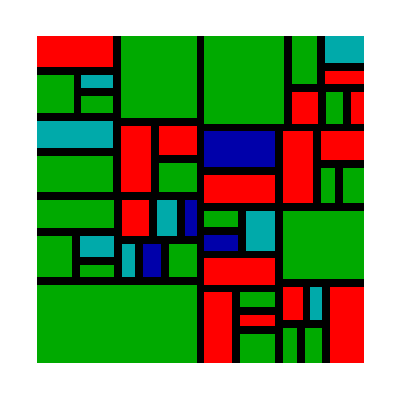

```mathematica
applyBlockType[#]&/@zeroBlocks;
ArrayPlot[MapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False]
```

### Give each block a height based on elevation noise

```mathematica
getElevationNoise[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]]]

Module[{blockType,initHeight},Table[blockType=MapGrid[[zeroBlocks[[x]][[1]]]][[zeroBlocks[[x]][[2]]]];initHeight=Floor[Rescale[getElevationNoise[zeroBlocks[[x]]],{0.30,0.7},{1,10}]];AppendTo[zeroBlocks[[x]],Which[blockType==tileToNumber["park"],1,blockType==tileToNumber["business"],Min[{Floor[2*initHeight],10}],blockType==tileToNumber["industrial"],Max[2,Floor[0.6*initHeight]],True,initHeight]],{x,zeroBlocks//Length}]];
```

```mathematica
blockHeightGiver[grid_,coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],h=coords//Last},ReplacePart[grid,{y_,a_,b_} /; (y>h&&x1<=a<=x2&&y1<=b<=y2)||(y>1&&grid[[y]][[a]][[b]]==1)->tileToNumber["background"]]]
```

### 3D visualization

```mathematica
numLevels=10;
MapGrid3D=Table[MapGrid,{x,numLevels}];
Table[MapGrid3D=blockHeightGiver[MapGrid3D,zeroBlocks[[i]]],{i,zeroBlocks//Length}];
```

```mathematica
ArrayPlot3D[MapGrid3D,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],BoxRatios->{1, 1,1}]
```

-Graphics3D-

## Spawn Entities on City Blocks

```mathematica
(*tileColors=<|"road"->Black,"background"->White,"park" -> Green, "residential"->Red,"industrial"->Darker[Green], "commercial"->Darker[Blue],"business"->Darker[Cyan]|>;
tileToNumber=AssociationThread[Keys[tileColors],{1,0,3,4,5,6,7}];*)
colors={White,Black,Gray,Green,Red,Darker[Green],Darker[Blue],Darker[Cyan],Cyan,Blue,Darker[Brown],Brown,Darker[Gray]};
colorData=Thread[Range[0,(colors//Length)-1]->colors];
emptyMapGrid=Table[0,{x,MapGrid//Length},{y,MapGrid[[1]]//Length}];
city3D=Prepend[Table[emptyMapGrid,49],MapGrid];
```

```mathematica
colorData
```

{0→GrayLevel[1],1→GrayLevel[0],2→GrayLevel[0.5],3→RGBColor[0, 1, 0],4→RGBColor[1, 0, 0],5→RGBColor[0, Rational[2, 3], 0],6→RGBColor[0, 0, Rational[2, 3]],7→RGBColor[0, Rational[2, 3], Rational[2, 3]],8→RGBColor[0, 1, 1],9→RGBColor[0, 0, 1],10→RGBColor[0.4, 0.2666666666666667, 0.13333333333333336],11→RGBColor[0.6, 0.4, 0.2],12→RGBColor[0.33333333333333337, 0.33333333333333337, 0.33333333333333337]}

```mathematica
Thread[Values[tileToNumber]->Values[tileColors]]
```

{1→GrayLevel[0],0→GrayLevel[1],3→RGBColor[0, 1, 0],4→RGBColor[1, 0, 0],5→RGBColor[0, Rational[2, 3], 0],6→RGBColor[0, 0, Rational[2, 3]],7→RGBColor[0, Rational[2, 3], Rational[2, 3]]}

#### entity defs

```mathematica
tree={
{{0,0,0},
{0,10,0},
{0,0,0}},
{{0,0,0},
{0,10,0},
{0,0,0}},
{{0,5,0},
{5,5,5},
{0,5,0}},
{{0,0,0},
{0,5,0},
{0,0,0}}};
house={
{{11,11,11},
{11,11,11},
{11,10,11}},
{{11,11,11},
{11,11,11},
{11,10,11}},
(*{{11,11,11},
{11,11,11},
{11,11,11}},*)
{{10,10,10},
{10,10,10},
{10,10,10}},
{{0,10,0},
{0,10,0},
{0,10,0}}};
apartment={
{{2,2,2},
{2,2,2},
{2,2,2},
{2,2,2}},
{{8,2,8},
{2,2,2},
{2,2,2},
{8,2,8}},
{{2,2,2},
{2,2,8},
{8,2,2},
{2,2,2}},
{{8,2,8},
{2,2,2},
{2,2,2},
{8,2,8}},
{{2,2,2},
{8,2,2},
{2,2,8},
{2,2,2}},
{{8,2,8},
{2,2,2},
{2,2,2},
{8,2,8}},
{{2,2,2},
{2,2,2},
{2,2,2},
{2,2,2}}};
factory={
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}},
{{12,9,12,9,12},
{9,12,12,12,9},
{12,12,12,12,12},
{9,12,12,12,9},
{12,9,12,9,12}},
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}},
{{12,9,12,9,12},
{9,12,12,12,9},
{12,12,12,12,12},
{9,12,12,12,9},
{12,9,12,9,12}},
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}},
{{12,9,12,9,12},
{9,12,12,12,9},
{12,12,12,12,12},
{9,12,12,12,9},
{12,9,12,9,12}},
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}},
{{12,9,12,9,12},
{9,12,12,12,9},
{12,12,12,12,12},
{9,12,12,12,9},
{12,9,12,9,12}},
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}}};
{{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},(*level 1 part 1*)
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},(*level 1 part 1*)
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}}, (*level 1 part 2*)
{{0,0,0,0,0,0,0,0,0,0},(*level 2 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},(*level 2 ends*)
{{0,0,0,0,0,0,0,0,0,0},(*level 2 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},(*level 2 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},(*level 2 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},(*level 3 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,12,12,0,0,0,0},
{0,0,0,0,12,12,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,12,12,0,0,0,0},
{0,0,0,0,12,12,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}}}//Iconize
```

```mathematica
skyscraper=;
```

### visual

```mathematica
Length@skyscraper
```

30

```mathematica
ArrayPlot3D[tree,ColorRules->colorData]
```

-Graphics3D-

```mathematica
city3D[[2;;5,1;;3,1;;3]]=tree;
city3D[[2;;5]][[4;;6]][[1;;3]]=house;
city3D[[2;;8]][[10;;13]][[1;;3]]=apartment;
city3D[[2;;10]][[20;;24]][[1;;5]]=factory;
city3D[[2;;31]][[30;;39]][[1;;10]]=skyscraper;
```

```mathematica
ArrayPlot3D[city3D,ColorRules->colorData,BoxRatios->{1, 1,0.25}]
```

-Graphics3D-

```mathematica
skyscraper//Length
```

30

### populating blocks with entities(buildings and trees)

```mathematica
parkEntities={tree};
residentialEntities={apartment,house};
businessEntities={skyscraper};
industrialEntities={factory};
commercialEntities={};
blockEntities={parkEntities,residentialEntities,industrialEntities,commercialEntities,businessEntities};
numToEntity=AssociationThread[{3,4,5,6,7},blockEntities];
```

func blockputter[type, coords,entity,biggestSize]:
position = jitter start
pick starting area jitter
	check size continue if too big
	PUT IT
	jitter x and da y

```mathematica
putEntity[coords_,entity_]:=Module[{x1=coords[[1]],y1=coords[[2]]},city3D[[2;;2+(entity//Length)-1,x1;;x1+(entity[[1]]//Length)-1,y1;;y1+(entity[[1,1]]//Length)-1]]=entity;];

spawnEntities[coords_,entity_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],z=3,bigBlockZero=Table[0,{(entity[[1]]//Length)},{(entity[[1,1]]//Length)}]},
Table[
If[
bigBlockZero==city3D[[z]][[i;;i+(entity[[1]]//Length)-1,j;;j+(entity[[1,1]]//Length)-1]]&&RandomReal[]<=0.22,
putEntity[{i,j},entity],0],
{i,x1,x2-(entity//Length),RandomInteger[{2,3}]},{j,y1,y2-(entity[[1]]//Length),RandomInteger[{2,3}]}];]
```

(* DO THE PUTTING ENTITIES THING FOR EACH BLOCK;*)
go to each block
check block type
need to give entity based on block type(but for residentaila
	given a list of entities(per block type)
	randomly select one(?)
	call da fackin function

```mathematica
Table[spawnEntities[zeroBlocks[[i]],RandomChoice[numToEntity[MapGrid[[zeroBlocks[[1]],zeroBlocks[[2]]]]]]],{i,zeroBlocks//Length}];
```

RandomChoice::lrwl: The items for choice Missing[KeyAbsent,{{4,5,1,5,4},{4,5,1,5,4},{4,5,1,5,4},{5,5,1,5,5},{4,5,1,5,4}}] should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

```mathematica
spawnEntities[{153,35,161,59},tree]
```

## Final Results

## Conclusion

## Future work

## Works Cited

Biagioli, Adrian. “Understanding Perlin Noise.” Adrian’s Soapbox, 9 Aug. 2014, https://adrianb.io/2014/08/09/perlinnoise.html. 
Spottedleaf. OldGenerator. GitHub, https://github.com/Spottedleaf/OldGenerator/.  
“An Algorithm for City Map Generation.” The Worldsmith Project, 22 June 2024, https://zero.re/worldsmith/roadnet/. 
“Block Assignment: Using Adjacency Tables.” The Worldsmith Project, 21 Aug. 2024, https://zero.re/worldsmith/blockassign/. 
“Noise Generator.” Minecraft Wiki, Fandom, https://minecraft.fandom.com/wiki/Noise_generator.